```mathematica
accuracy = 10^(-10);
inputFile = "problem3.txt";
outputFile = "W_out_Quick.txt";
```

```mathematica
hull = {};
SetDirectory["/Users/pinev/Desktop/practice/st"];
pairs = ReadList[inputFile, Real];
pairs = Delete[pairs,1];
pairs=Partition[pairs,2];
amtOfPoint = Length[pairs]
```

48

```mathematica
Precision[pairs[[1, 1]]]
```

20.289

```mathematica
LineL[p1_, p2_, p_] := (p[[1]]-p1[[1]])*(p2[[2]]-p1[[2]])-(p[[2]]-p1[[2]])*(p2[[1]]-p1[[1]]);
```

```mathematica
DetSide[p1_,p2_,p_]:=Module[{res,Side},

res:=LineL[p1, p2, p];
If[res<0, Side = 1, If[res > 0, Side = -1, 0]]; 

Side
]
```

```mathematica
LineDist[p1_,p2_,p_]:=Abs[LineL[p1, p2, p]];
```

```mathematica
QuickH[P_List, p1_, p2_, side_]:= Module[{currentI, maxDist, i, dist},
currentI = -1;
maxDist = 0;

For[i = 1, i <= amtOfPoint, ++i,

dist := LineDist[p1, p2, pairs[[i]]];
If[((DetSide[p1, p2, pairs[[i]]] == side) &&(dist > maxDist)),
currentI = i;
maxDist = dist;
]
];

If[(currentI == -1),
(*AppendTo[hull,p1];AppendTo[hull,p2];*)

If[(!(MemberQ[hull,p1])),AppendTo[hull,p1]];If[(!(MemberQ[hull,p2])),AppendTo[hull,p2]];

Return[]
];
QuickH[P, pairs[[currentI]], p1, -DetSide[pairs[[currentI]], p1, p2]];
QuickH[P, pairs[[currentI]], p2, -DetSide[pairs[[currentI]], p2, p1]];
]
```

```mathematica
calcHull[P_List]:=Module[{min, max, i},

If[amtOfPoint<3,Print["It's not possible to convex hull, amtOfPoint < 3";Abort]];

min = 1;
max = 1;

For[i = 2, i <= amtOfPoint, ++i, 
If[pairs[[i, 1]] < pairs[[min, 1]],
min = i;];
If[pairs[[i, 1]] > pairs[[max, 1]],
max = i;];
If[((Abs[(pairs[[i, 1]] - pairs[[min, 1]])] < accuracy) && (pairs[[i, 2]] < pairs[[min, 2]])),
min = i;];
If[((Abs[(pairs[[i, 1]] - pairs[[max, 1]])] < accuracy) && (pairs[[i, 2]] > pairs[[max, 2]])),
max = i;]
];

QuickH[P, pairs[[min]], pairs[[max]], 1];
QuickH[P, pairs[[min]], pairs[[max]], -1];

center = {0, 0};
For[i = 1, i <= amtOfPoint, ++i,
center[[1]]+= pairs[[i, 1]];
center[[2]] += pairs[[i, 2]];
];

center[[1]] = center[[1]] / Length[hull];
center[[2]] = center[[2]] / Length[hull];

Atan2[p_]:=ArcTan[p[[2]], p[[1]]];
CustomCompare[p1_,p2_]:=Atan2[p1 - center]<Atan2[p2-center];
hull=Sort[hull, CustomCompare];

str =StringReplace[ToString[SetPrecision[hull,17]] ,{ "{"->"", "}, "->"\n", ","->"", "}}" ->""}];
     str=StringJoin[{ToString[Length[hull]], "\n",str}];
     Export[outputFile, str];

gHull = hull;
AppendTo[gHull,gHull[[1]]];
Graphics[{Point@P, Line@gHull}]
]
```

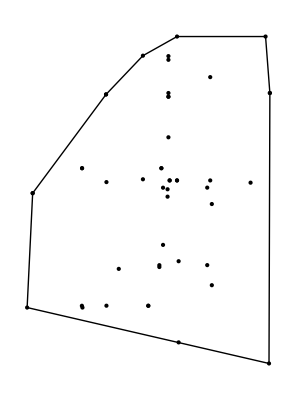
{0.015625,-Graphics-}

```mathematica
time=Timing[calcHull[pairs]]
```

```mathematica
time[[1]]
```

0.015625

```mathematica
(*calcHull[pairs]*)
```

```mathematica
hull
```

{{-75.3200803742173841,-68.5810899295731118},{-72.3200803742173841,-6.5810899295731118},{-32.5408,46.94682940555158},{-12.5408,67.94682940555158},{5.9455434948910598351,78.323776515877549858},{53.945235434948910598351,78.323776515877549858},{56.282290700875986,47.7084251701634474},{55.8154210985726405,-98.8894682341759812062034}}

```mathematica
Length[hull]
```

8

```mathematica
gHull
```

{{-75.3200803742173841,-68.5810899295731118},{-72.3200803742173841,-6.5810899295731118},{-32.5408,46.94682940555158},{-12.5408,67.94682940555158},{5.9455434948910598351,78.323776515877549858},{53.945235434948910598351,78.323776515877549858},{56.282290700875986,47.7084251701634474},{55.8154210985726405,-98.8894682341759812062034},{-75.3200803742173841,-68.5810899295731118}}